```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

## Importing data

```mathematica
(*numerical solution, flag == 0,
 exact solution, flag == 1 and 
error flag == 2*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]]
];

result = Import[filename,"Table"][[2;;-1,All]]
]
```

## IDs for different variables

```mathematica
(*we declare the IDs for different variables, this will help us with plotting*)
IDSpace = 1;
IDRho = 1+IDSpace;
IDvx = 2+IDSpace;
IDtheta = 3+IDSpace;
```

## Mapping to Primitive variables

```mathematica
(*we change the numerical solution obtained to the primitive variables.*)
ConvToPrim[sol_]:=Module[{factorθ,factorσ,factorq,trialsol},
trialsol = sol;
factorθ = √2;
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;

trialsol
]
```

## Poisson Heat conduction

### G20

```mathematica
ndof=24576;
foldername = "Tests/build/output_N6_N8_poisson_heat_conduction_1D_Kn0p1";
Error20=importdata[ndof,1,"_global_",2,foldername];
Error20 = ConvToPrim[Error20];
```

#### θ

```mathematica
plot1=ListPlot[Error20⟦All,{1,IDtheta}⟧,Joined->True];
```

### M Adaptive

#### Single system

```mathematica
ndof=4096;
foldername = "Tests/build/output_N6_N8_N12_poisson_heat_1D_Kn0p1";
SolN8=importdata[ndof,1,"_global_",0,foldername];
SolN8 = ConvToPrim[SolN8];
```

#### Adapted system

```mathematica
ndof=16360;
foldername = "Tests/build/output_N6_N8_N12_poisson_heat_1D_Kn0p1";
ErrorN6N8=importdata[ndof,1,"_global_",2,foldername];
ErrorN6N8 = ConvToPrim[ErrorN6N8];
```

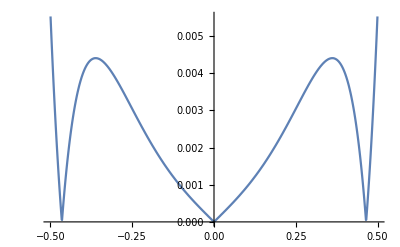

```mathematica
plotSingle=ListPlot[ErrorN8⟦All,{1,IDtheta}⟧,Joined->True]
```

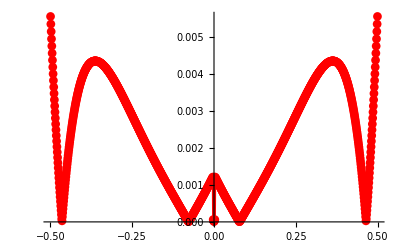

```mathematica
plotAdaptive = ListPlot[ErrorN6N8⟦All,{1,IDtheta}⟧,Joined->True,PlotStyle->Red,PlotMarkers->Automatic]
```

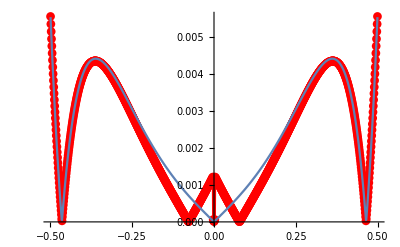

```mathematica
Show[plotAdaptive,plotSingle]
```